# Electrokinetics

```mathematica
ClearAll["Global`*"]
```

## Operators

Gradient

```mathematica
grad=Function[f, {D[f,r],D[f,θ]/r} // Simplify];
```

Divergence

```mathematica
div = Function[{F}, D[r^2 F[[1]],r]/r^2+D[Sin[θ]F[[2]],θ]/(r Sin[θ])// Simplify];
```

Scalar Laplacian

```mathematica
slapl=Function[f,div[grad[f]]];
```

Vector Laplacian

```mathematica
vlapl = Function[F, {
slapl[F[[1]]] - 2 F[[1]]/r^2-2 D[F[[2]]Sin[θ],θ]/(r^2 Sin[θ]),
slapl[F[[2]]]-F[[2]]/(r Sin[θ])^2 + 2 D[F[[1]],θ]/r^2} // Simplify];
```

Solution for zero-force Stokes flow, for β1:

```mathematica
v=β{(1-1/r^3)Cos[θ],-(1+1/(2 r^3))Sin[θ]};
{vlapl[v], div[v]}
```

{{0,0},0}

```mathematica
{v/. r->Infinity, v /.r->1}
```

{{β Cos[θ],-β Sin[θ]},{0,-3/2 β Sin[θ]}}

Force on a sphere due to Newtonian stress:

```mathematica
stress = Function[{p, v}, {-p + 2D[v[[1]], r], 
D[v[[2]], r]+(D[v[[1]],θ] - v[[2]])/r} /. r -> 1];
force = Function[{p, v}, stress[p,v] // Simplify];
```

```mathematica
p = 0; f = stress[p, v]. {Cos[θ],-Sin[θ] // Simplify}
```

6 β Cos[θ]^2-3 β Sin[θ]^2

Total force:

```mathematica
Integrate[ 2Pi f Sin[θ],{θ,0,Pi}]
```

0

```mathematica
c=1+ (3β)/(4 r^2)Cos[θ]; ϕ = β(1/(4 r^2)-r)Cos[θ];
{slapl[c], slapl[ϕ]} 
Series[Log[c]+ϕ,{β,0,2}]/.r->1 
Series[D[c, r]- c D[ϕ, r], {β,0, 2}]/.r->1 // Simplify
```

{0,0}

-9/32 Cos[θ]^2 β^2+O[β]^3

9/8 Cos[θ]^2 β^2+O[β]^3

Solution of Poisson equations for c and ϕ

```mathematica
c=1+ (3β)/(4 r^2)Cos[θ]; ϕ = β(1/(4 r^2)-r)Cos[θ];v  =β{(1-1/r^3)Cos[θ],-(1+1/(2 r^3))Sin[θ]};
RHS1 = Simplify[-grad[c].grad[ϕ]]
RHS2 = Simplify[v . grad[c]]
RHS3=slapl[ϕ] grad[ϕ]
```

-(3 β^2 (5+4 r^3+3 (1+4 r^3) Cos[2 θ]))/(32 r^6)

-(3 β^2 (-5+2 r^3+(-3+6 r^3) Cos[2 θ]))/(16 r^6)

{0,0}

```mathematica
ϕ2 = 3/32 β^2(2 Cos[2θ]/r-(1+Cos[2θ])/(2 r^4));slapl[ϕ2]==RHS1
c2=3/16 β^2(Cos[2θ]/r+(1+Cos[2θ])/(2 r^4));slapl[c2]==RHS2
```

True

True

Zero net force from quaratic term in Maxwell stress

```mathematica
ϕ
f = grad[ϕ](grad[ϕ].{1,0}) - (grad[ϕ].grad[ϕ])/2{1,0} /. r->1
f = Simplify[f . {Cos[θ],-Sin[θ]}]
Integrate[2 π f Sin[θ], {θ, 0 , π}]
```

(1/(4 r^2)-r) β Cos[θ]

{9/4 β^2 Cos[θ]^2+1/2 (-9/4 β^2 Cos[θ]^2-9/16 β^2 Sin[θ]^2),-9/8 β^2 Cos[θ] Sin[θ]}

9/128 β^2 (15 Cos[θ]+Cos[3 θ])

0

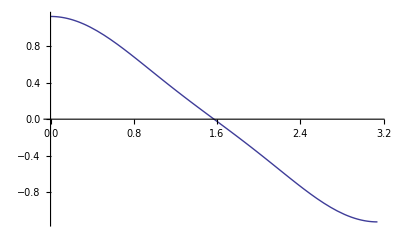

```mathematica
Plot[f /. β-> 1, {θ,0,Pi}]
```

## Testing

```mathematica
ϕ=-β(1/r)Cos[θ];
D[ϕ,r]/.r->1
D[ϕ,r]/.r->∞
```

β Cos[θ]

0

```mathematica
F=grad[ϕ](grad[ϕ].{1,0})-{1,0}(grad[ϕ].grad[ϕ])/2 /. r->1// Simplify
f = F . {Cos[θ],-Sin[θ]} // Simplify
Integrate[f*2*Pi*Sin[θ],{θ,0,π}]
```

{1/2 β^2 Cos[2 θ],β^2 Cos[θ] Sin[θ]}

1/2 β^2 Cos[θ] (-1+2 Cos[2 θ])

0

```mathematica
Log[1-Tanh[Log[x]/4]^2]//Simplify
```

```mathematica
D[Log[Sech[Log[x]/4]^2],x]
```

-Tanh[Log[x]/4]/(2 x)

```mathematica
D[2Log[1-Tanh[Log[c/g]/4]^2],c]//Simplify
```

-Tanh[1/4 Log[c/g]]/c